# Quantum-Phase Estimation: Implementation

Episode 32. Quantum Fourier Transform: Principle

Episode 33. Quantum Fourier Transform: Implementation

Episode 34. Controlled Power

Episode 35. Quantum Phase Estimation: Principle

Episode 36. Quantum Phase Estimation: Implementation

## What to study?

Through these two episodes, one can examine the following key questions concerning quantum computing:

Why is quantum computer faster than classical computer (if at all)?

Why is it difficult to find quantum algorithms exhibiting quantum supremacy?

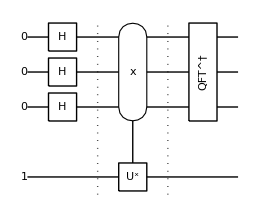

Figure 1. A schematic quantum circuit for quantum phase estimation, which illustrates the typical structure of quantum algorithms.

## Quantum Implementation

```mathematica
$n=3;
kk=Range[$n];
Let[Qubit,S,T]
```

```mathematica
qc=QuantumCircuit[
Ket[S@kk],Ket[T->1],
S[kk,6],"Separator",
ControlledExp[S[kk],Phase[ϕ,T[3]]],"Separator",
Dagger@QFT[S[kk]],
"Invisible"->{S[$n+1/2]}
]
```

```mathematica
Block[
{ϕ=2Pi*3/2^$n},
EchoTiming[out=FullSimplify@Elaborate[qc];];
ProductForm[out,{S[kk],T}]
]
```

1.07798

```mathematica
new=QuantumCircuit[
Ket[S@kk],Ket[T->1],
S[kk,6],"Separator",
Expand@ControlledExp[S[kk],Phase[ϕ,T[3]]],"Separator",
Expand@Dagger@QFT[S[kk]],
"Invisible"->{S[$n+1/2]}
]
```

## Summary

### Keywords

Quantum supremacy, quantum superpower

Quantum super-weakness

Quantum Fourier transform

### Functions

ControlledGate

ControlledExp

QFT

### Related Links

Section 4.4 of the Quantum Workbook (2022, 2023).

Tutorial: Quantum Phase Estimation

Tutorial: Order-Finding Algorithm